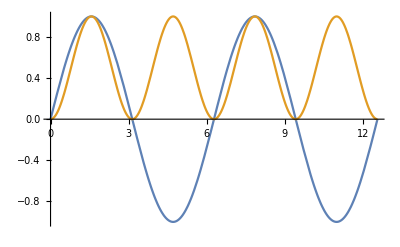

```mathematica
Plot[{Sin[t],Sin[t]^2},{t,0,4*Pi}]
```

```mathematica
avgF[T_]:=N[1/T*Integrate[Sin[t]^2,{t,0,T}]]
```

```mathematica
avgF[100]
```

0.502183

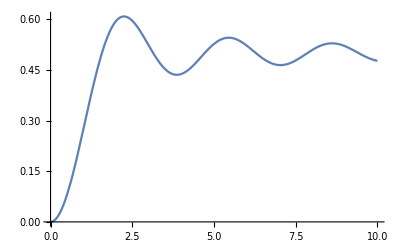

```mathematica
Plot[avgF[T],{T,0.000001,10}, PlotRange->Full]
```

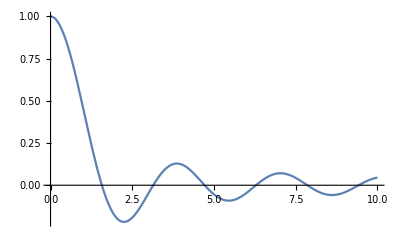

```mathematica
Plot[Sinc[T]*Cos[T],{T,0.000001,10}, PlotRange->Full]
```